```mathematica
控制器设计测试：YAW_RATE
```

```mathematica
(*飞机姿态线性化后*)
Myaw = 
Equs= {D[yaw[t],t]==Myaw};
```

```mathematica
{{(*起飞模型*)}, {Equs={
D[height[t],{t,2}]==24*th^2-m*g
};
(*t from 0 -> 1 *)
LaplaceTransform[Equs,t,s]/.{m->1.2,g->9.8}}}
```

{{Null},{{Null (-s height[0]+s^2 LaplaceTransform[height[t],t,s]-height'[0]==(-11.76+24 th^2)/s)}}}

```mathematica
Y=(24*ths)/s^3;
T=24/s^3; 
trans=TransferFunctionModel[T,s];
 pid= PIDTune[trans,"PID","PIDData"]["FeedbackIdealParameters"]
```

{-0.294512,1.76761,0.707128}

```mathematica
PID
```

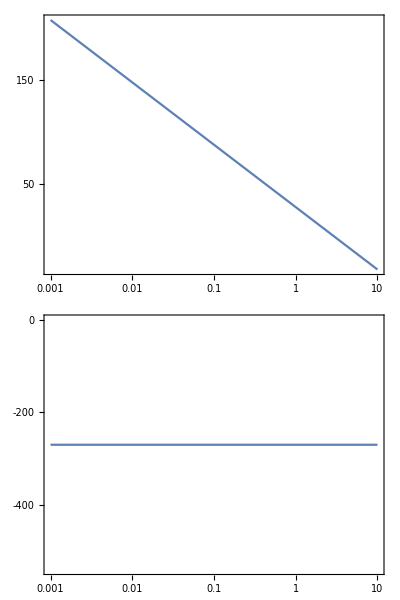

```mathematica
BodePlot[T]
```